Det матрицы = 10.5975

Минор матрицы, который может быть отрицателен = 0.2355

К граничное, Должно быть больше kp*k0 = 45 ) = 102.439

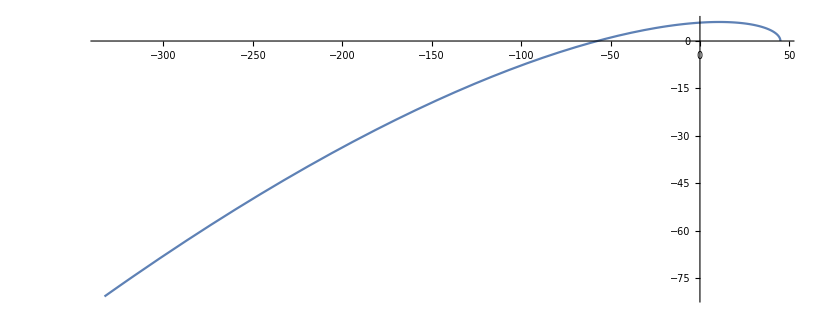

```mathematica
T0 = 0.41;
T1 = 0.01;
T2 = 0.1;
k0 = 10;
kp = 4.5;

(*----------------- O1-P1 -----------------*)
a3 = T0*T1;
a2 = T1+T0;
a1 = 1;
a0 =kp*k0;

Print["Det матрицы = ",Det[({{a2, a0, 0}, {a3, a1, 0}, {0, a2, a0}})]]
Print["Минор матрицы, который может быть отрицателен = ", Det[({{a2, a0}, {a3, a1}})]]
Print["К граничное, Должно быть больше kp*k0 = 45 ) = ",(a1*a2)/a3 ]
ParametricPlot[{Re[a3*(I*w)^3+a2*(I*w)^2+a1*(I*w)+a0],Im[a3*(I*w)^3+a2*(I*w)^2+a1*(I*w)+a0]},{w,0,30}]


(*----------------------------------------*)
```

```mathematica
(*----------------- O1-P2 -----------------*)
```

Det матрицы = 95.6475

Минор матрицы, который может быть отрицателен = 2.1255

К граничное, Должно быть больше kp*k0 = 45 ) = 563.415

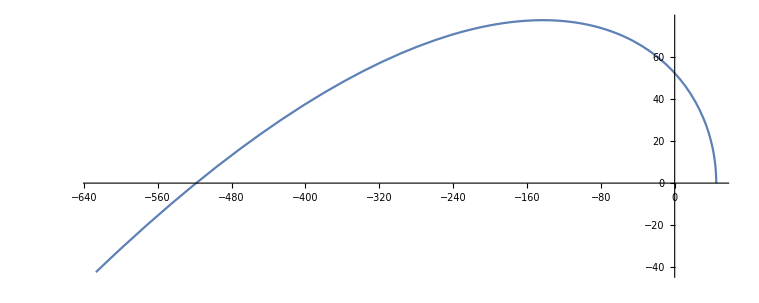

```mathematica
a3 = T0*T1;
a2 = T1+T0;
a1 = 1+kp*k0*T2;
a0 =kp*k0;

Print["Det матрицы = ",Det[({{a2, a0, 0}, {a3, a1, 0}, {0, a2, a0}})]]
Print["Минор матрицы, который может быть отрицателен = ", Det[({{a2, a0}, {a3, a1}})]]
Print["К граничное, Должно быть больше kp*k0 = 45 ) = ",(a1*a2)/a3 ]
ParametricPlot[{Re[a3*(I*w)^3+a2*(I*w)^2+a1*(I*w)+a0],Im[a3*(I*w)^3+a2*(I*w)^2+a1*(I*w)+a0]},{w,0,40}]

(*----------------------------------------*)
```

```mathematica
(*----------------- O2-P1 -----------------*)
```

Det матрицы = -27.2025

Минор матрицы, который может быть отрицателен = -0.6045

К граничное, Должно быть больше kp*k0 = 45 ) = -102.439

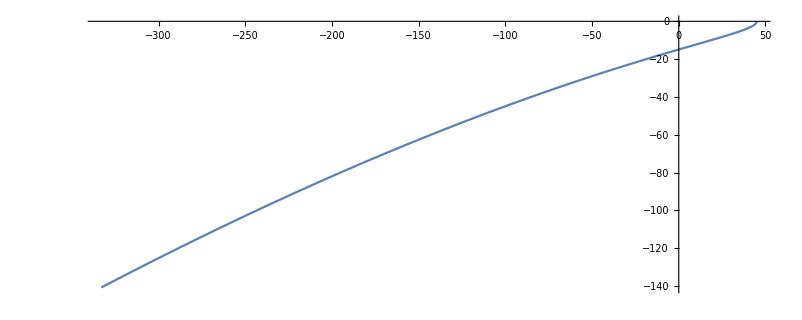

```mathematica
a3 = T0*T1;
a2 = T1+T0;
a1 = -1;
a0 =kp*k0;

Print["Det матрицы = ",Det[({{a2, a0, 0}, {a3, a1, 0}, {0, a2, a0}})]]
Print["Минор матрицы, который может быть отрицателен = ", Det[({{a2, a0}, {a3, a1}})]]
Print["К граничное, Должно быть больше kp*k0 = 45 ) = ",(a1*a2)/a3 ]
ParametricPlot[{Re[a3*(I*w)^3+a2*(I*w)^2+a1*(I*w)+a0],Im[a3*(I*w)^3+a2*(I*w)^2+a1*(I*w)+a0]},{w,0,30}]
(*----------------------------------------*)
```

Det матрицы = 57.8475

Минор матрицы, который может быть отрицателен = 1.2855

К граничное, Должно быть больше kp*k0 = 45 ) = 358.537

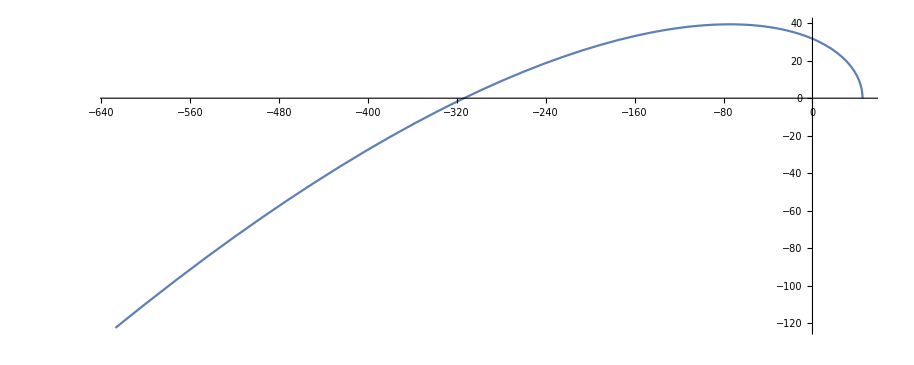

```mathematica
(*----------------- O2-P2 -----------------*)
a3 = T0*T1;
a2 = T1+T0;
a1 = T2*kp*k0-1;
a0 =kp*k0;

Print["Det матрицы = ",Det[({{a2, a0, 0}, {a3, a1, 0}, {0, a2, a0}})]]
Print["Минор матрицы, который может быть отрицателен = ", Det[({{a2, a0}, {a3, a1}})]]
Print["К граничное, Должно быть больше kp*k0 = 45 ) = ",(a1*a2)/a3 ]
ParametricPlot[{Re[a3*(I*w)^3+a2*(I*w)^2+a1*(I*w)+a0],Im[a3*(I*w)^3+a2*(I*w)^2+a1*(I*w)+a0]},{w,0,40}]
(*----------------------------------------*)
```